## Lesson

Make a 2D array of values:

```mathematica
Table[x,4,5]
```

{{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x}}

Lay out values from an array in a grid:

```mathematica
Grid[Table[i+j,{i,5},{j,5}]]
```

2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9
6 | 7 | 8 | 9 | 10

Visualize the values in an array:

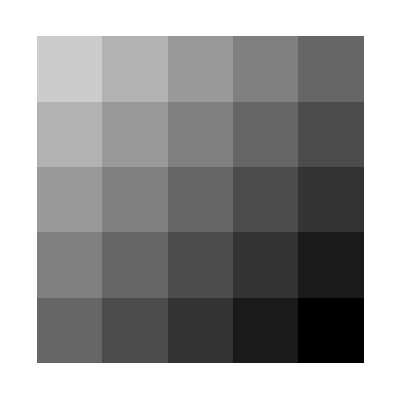

```mathematica
ArrayPlot[Table[i+j,{i,5},{j,5}]]
```

Get the array of pixel values from an image:

```mathematica
ImageData[Binarize[Rasterize["W"]]]
```

{{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1,0,1},{0,0,1,1,1,1,1,1,0,0,1},{0,0,1,1,1,1,1,1,0,0,1},{1,0,1,1,0,0,1,1,0,0,1},{1,0,1,1,0,0,1,1,0,0,1},{1,0,1,1,0,0,1,1,0,1,1},{1,0,1,1,0,0,0,1,0,1,1},{1,0,0,0,0,1,0,1,0,1,1},{1,0,0,0,1,1,0,1,0,1,1},{1,0,0,0,1,1,0,0,0,1,1},{1,1,0,0,1,1,0,0,0,1,1},{1,1,0,0,1,1,1,0,0,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1}}

## Questions

Q1. Make a 12×12 multiplication table.

```mathematica
Table[i j,{i,12},{j,12}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12},{2,4,6,8,10,12,14,16,18,20,22,24},{3,6,9,12,15,18,21,24,27,30,33,36},{4,8,12,16,20,24,28,32,36,40,44,48},{5,10,15,20,25,30,35,40,45,50,55,60},{6,12,18,24,30,36,42,48,54,60,66,72},{7,14,21,28,35,42,49,56,63,70,77,84},{8,16,24,32,40,48,56,64,72,80,88,96},{9,18,27,36,45,54,63,72,81,90,99,108},{10,20,30,40,50,60,70,80,90,100,110,120},{11,22,33,44,55,66,77,88,99,110,121,132},{12,24,36,48,60,72,84,96,108,120,132,144}}

Q2. Make a 5×5 multiplication table for Roman numerals.

```mathematica
Table[RomanNumeral[i j],{i,5},{j,5}]
```

{{I,II,III,IV,V},{II,IV,VI,VIII,X},{III,VI,IX,XII,XV},{IV,VIII,XII,XVI,XX},{V,X,XV,XX,XXV}}

Q3. Make a 10×10 grid of random colours.

```mathematica
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.1020537837753781, 0.9355224121049441, 0.277188349666212] | RGBColor[0.6726794800276052, 0.8369303015205611, 0.16061376321084464] | RGBColor[0.4637792176733133, 0.0017184080849304006, 0.5508734993181972] | RGBColor[0.21834968850570546, 0.8838295263163094, 0.36438407134395345] | RGBColor[0.1355020731948271, 0.7068583550655521, 0.34529474413762395] | RGBColor[0.7334846926049983, 0.47240075033838447, 0.3229425175329357] | RGBColor[0.4581769094958428, 0.6321328328750233, 0.5833398415229512] | RGBColor[0.06010999914057691, 0.6797841518069332, 0.9092849573273212] | RGBColor[0.040227889589895094, 0.6948640635986565, 0.8103150600998537] | RGBColor[0.8397977776003904, 0.13515320062157699, 0.7421464666951678]
RGBColor[0.15845027522279054, 0.34502272438237025, 0.4819112445744287] | RGBColor[0.8588616160594986, 0.043117250330727996, 0.1348153659322986] | RGBColor[0.5889192036744384, 0.07649888205951827, 0.500419763914274] | RGBColor[0.8225424772753669, 0.21701113698438612, 0.14378207144528843] | RGBColor[0.5181688272079326, 0.25890472345938886, 0.5809763619772759] | RGBColor[0.8782775041725901, 0.39723832456341834, 0.6582147834752063] | RGBColor[0.7362004072163568, 0.8106862061298721, 0.5312613026095416] | RGBColor[0.504808997694981, 0.5267322328000397, 0.0020245427216580847] | RGBColor[0.7027991650301408, 0.34413569826443235, 0.13953084830206208] | RGBColor[0.7333203786751636, 0.7619383070651757, 0.9735640338161042]
RGBColor[0.38662202433575965, 0.9948949239103642, 0.05672984924612523] | RGBColor[0.7504859729279678, 0.8690314575542295, 0.7533408769225372] | RGBColor[0.8076563084567752, 0.09553425641545421, 0.45024296726549284] | RGBColor[0.5656817617719503, 0.5420906670054637, 0.02168471917145398] | RGBColor[0.5817876803227358, 0.6027293589978522, 0.7887765482614302] | RGBColor[0.15973908626487532, 0.8626389479031704, 0.9629355990574702] | RGBColor[0.6361959882353303, 0.12565903049773475, 0.660031537343883] | RGBColor[0.26789798055478964, 0.6236638763791484, 0.5283249891657069] | RGBColor[0.3920634936141081, 0.42113736169018967, 0.7703659348562595] | RGBColor[0.6719599920205372, 0.15666293093037087, 0.5373569153904096]
RGBColor[0.993465752226335, 0.2561925188665992, 0.8096949620984588] | RGBColor[0.7576068524983597, 0.5502111764787685, 0.039224326774900176] | RGBColor[0.13004073114269654, 0.1666070327955309, 0.1905274942356885] | RGBColor[0.5718122787994588, 0.8000791218139625, 0.7397283260415757] | RGBColor[0.9487792789309035, 0.798017390479681, 0.624445554475813] | RGBColor[0.2764368896567504, 0.6989325973937042, 0.5237847719349775] | RGBColor[0.15889226654668254, 0.8320078927707779, 0.2562482284821934] | RGBColor[0.8247696158702553, 0.9126902059844939, 0.6625099727075214] | RGBColor[0.8098988128522195, 0.32093536278459744, 0.06458057679401885] | RGBColor[0.030460266584160234, 0.5036955677956563, 0.5376099477855252]
RGBColor[0.5047152684086886, 0.07024262222322952, 0.39578459530604926] | RGBColor[0.3597971408888503, 0.9862350623040319, 0.07916373914827934] | RGBColor[0.6204784145671403, 0.03143359230699305, 0.686868790275819] | RGBColor[0.06925143955246416, 0.7558521796692979, 0.16916997121590316] | RGBColor[0.65528219258314, 0.6251192487608104, 0.652089308827775] | RGBColor[0.6440931873641373, 0.0916495085899296, 0.784695488887936] | RGBColor[0.013734302399315279, 0.5621134409153625, 0.3153556836790934] | RGBColor[0.04796113660052326, 0.436118279274035, 0.16699262831285377] | RGBColor[0.1369222932046683, 0.11888317201976961, 0.9911571441342326] | RGBColor[0.5741861156165515, 0.6786995187201001, 0.3362576362123344]
RGBColor[0.3030199230949393, 0.4688828358537944, 0.8674261859871821] | RGBColor[0.41182946136954013, 0.586060077987137, 0.2526893196674831] | RGBColor[0.8405231461522928, 0.05038405830860304, 0.5002106987567705] | RGBColor[0.24231340307150817, 0.9940321554089946, 0.4120574877058485] | RGBColor[0.023982755045443005, 0.3444865461748696, 0.3660390388788437] | RGBColor[0.2556454586162702, 0.826092001807313, 0.6937606975895421] | RGBColor[0.442342518980799, 0.41226380721755507, 0.6058545817144982] | RGBColor[0.6192000979770504, 0.2743538018894267, 0.24982937375967929] | RGBColor[0.7997616041030793, 0.04897757702237904, 0.602489480989713] | RGBColor[0.8691327072278272, 0.5168240113956821, 0.008688708493352904]
RGBColor[0.040810585641160024, 0.022450717909454854, 0.9997937818931386] | RGBColor[0.4040315788516404, 0.18404687783159912, 0.7299746541162133] | RGBColor[0.9835772377331498, 0.08449983174645648, 0.6548494004463687] | RGBColor[0.9508350115035678, 0.6488416941905426, 0.4307586190960997] | RGBColor[0.5053460901072551, 0.14362444091891402, 0.2950404156591293] | RGBColor[0.03332047003795302, 0.1623594004661979, 0.5469235502494809] | RGBColor[0.8956739903632565, 0.008322055387142369, 0.7295416950438605] | RGBColor[0.35896728916995135, 0.6980738201495285, 0.7001407895169587] | RGBColor[0.20959452778426635, 0.7716822827013632, 0.3419959522528935] | RGBColor[0.08326872575361666, 0.5486141961423916, 0.7046004927229355]
RGBColor[0.16885260740852281, 0.09487257821443884, 0.3917646036376192] | RGBColor[0.8284611131924902, 0.46837971632583986, 0.008721971089044045] | RGBColor[0.6513308517589997, 0.023191855872795264, 0.904851174222921] | RGBColor[0.6673654235287592, 0.03473744294442471, 0.6548406154406681] | RGBColor[0.6748469266712316, 0.9283864402903228, 0.031693098170842315] | RGBColor[0.35449958231081813, 0.1320066801002313, 0.06117967648046996] | RGBColor[0.9385144301135764, 0.5244093495523641, 0.8256485011875774] | RGBColor[0.3458917515624995, 0.09693055732337341, 0.5542407711577713] | RGBColor[0.6778264725791703, 0.24644360601765292, 0.7719108161271473] | RGBColor[0.6493854334175226, 0.798693215039187, 0.7946477296523156]
RGBColor[0.3018482247335754, 0.5883085726687234, 0.11124939429874936] | RGBColor[0.046707831609653194, 0.6955730271320986, 0.2884417807243236] | RGBColor[0.13322523833792688, 0.7503870438661249, 0.9185543391792734] | RGBColor[0.33412502763174246, 0.5793029246838897, 0.15804439153873706] | RGBColor[0.14786439305429955, 0.412145415260573, 0.7125315611792529] | RGBColor[0.06293748451415393, 0.7108795942055803, 0.29437308574635357] | RGBColor[0.916429527916919, 0.2180224369803223, 0.6838528153681671] | RGBColor[0.1141300061417263, 0.7064420940711942, 0.1384440483372873] | RGBColor[0.13599802489597734, 0.05665149859510299, 0.6732554799310895] | RGBColor[0.16554190716744488, 0.8189272495649287, 0.6149867125282782]
RGBColor[0.6632771738954908, 0.02213603962693611, 0.08469216416696157] | RGBColor[0.3345560820103619, 0.47561436489174613, 0.9311627029110932] | RGBColor[0.11774164912528295, 0.9000995614178531, 0.921626139528511] | RGBColor[0.3236333148703818, 0.2556559193191339, 0.513856427696018] | RGBColor[0.3614249096490201, 0.26312465865601675, 0.5363024549313302] | RGBColor[0.11664118030132409, 0.33388683823962806, 0.687553370533426] | RGBColor[0.8301612932129341, 0.7868055499442674, 0.7240655210628899] | RGBColor[0.1892496030622035, 0.7723891601372588, 0.08921378593748375] | RGBColor[0.8309404540080045, 0.47901029520983784, 0.22665272742669562] | RGBColor[0.5258518279897293, 0.8466196801302135, 0.8580031545871563]

Q4. Make a 10×10 grid of randomly coloured random integers between 0 and 10.

```mathematica
Grid[Table[Style[RandomInteger[10],RandomColor[]],10,10]]
```

9 | 1 | 0 | 6 | 6 | 3 | 1 | 10 | 0 | 9
2 | 0 | 6 | 7 | 9 | 5 | 9 | 1 | 4 | 4
2 | 10 | 5 | 10 | 5 | 9 | 9 | 3 | 9 | 1
7 | 8 | 9 | 0 | 2 | 4 | 9 | 7 | 4 | 8
5 | 8 | 0 | 9 | 10 | 3 | 6 | 5 | 10 | 9
7 | 1 | 2 | 2 | 7 | 0 | 7 | 4 | 0 | 8
5 | 10 | 1 | 9 | 2 | 6 | 9 | 7 | 2 | 6
0 | 0 | 10 | 10 | 0 | 9 | 10 | 9 | 4 | 10
6 | 1 | 10 | 0 | 5 | 9 | 4 | 3 | 7 | 10
7 | 7 | 9 | 6 | 7 | 0 | 2 | 1 | 2 | 8

Q5. Make a grid of all possible strings consisting of pairs of letters of the alphabet (“aa”, “ab”, etc.).

```mathematica
Grid[Table[i<>j,{i,Alphabet[]},{j,Alphabet[]}]]
```

aa | ab | ac | ad | ae | af | ag | ah | ai | aj | ak | al | am | an | ao | ap | aq | ar | as | at | au | av | aw | ax | ay | az
ba | bb | bc | bd | be | bf | bg | bh | bi | bj | bk | bl | bm | bn | bo | bp | bq | br | bs | bt | bu | bv | bw | bx | by | bz
ca | cb | cc | cd | ce | cf | cg | ch | ci | cj | ck | cl | cm | cn | co | cp | cq | cr | cs | ct | cu | cv | cw | cx | cy | cz
da | db | dc | dd | de | df | dg | dh | di | dj | dk | dl | dm | dn | do | dp | dq | dr | ds | dt | du | dv | dw | dx | dy | dz
ea | eb | ec | ed | ee | ef | eg | eh | ei | ej | ek | el | em | en | eo | ep | eq | er | es | et | eu | ev | ew | ex | ey | ez
fa | fb | fc | fd | fe | ff | fg | fh | fi | fj | fk | fl | fm | fn | fo | fp | fq | fr | fs | ft | fu | fv | fw | fx | fy | fz
ga | gb | gc | gd | ge | gf | gg | gh | gi | gj | gk | gl | gm | gn | go | gp | gq | gr | gs | gt | gu | gv | gw | gx | gy | gz
ha | hb | hc | hd | he | hf | hg | hh | hi | hj | hk | hl | hm | hn | ho | hp | hq | hr | hs | ht | hu | hv | hw | hx | hy | hz
ia | ib | ic | id | ie | if | ig | ih | ii | ij | ik | il | im | in | io | ip | iq | ir | is | it | iu | iv | iw | ix | iy | iz
ja | jb | jc | jd | je | jf | jg | jh | ji | jj | jk | jl | jm | jn | jo | jp | jq | jr | js | jt | ju | jv | jw | jx | jy | jz
ka | kb | kc | kd | ke | kf | kg | kh | ki | kj | kk | kl | km | kn | ko | kp | kq | kr | ks | kt | ku | kv | kw | kx | ky | kz
la | lb | lc | ld | le | lf | lg | lh | li | lj | lk | ll | lm | ln | lo | lp | lq | lr | ls | lt | lu | lv | lw | lx | ly | lz
ma | mb | mc | md | me | mf | mg | mh | mi | mj | mk | ml | mm | mn | mo | mp | mq | mr | ms | mt | mu | mv | mw | mx | my | mz
na | nb | nc | nd | ne | nf | ng | nh | ni | nj | nk | nl | nm | nn | no | np | nq | nr | ns | nt | nu | nv | nw | nx | ny | nz
oa | ob | oc | od | oe | of | og | oh | oi | oj | ok | ol | om | on | oo | op | oq | or | os | ot | ou | ov | ow | ox | oy | oz
pa | pb | pc | pd | pe | pf | pg | ph | pi | pj | pk | pl | pm | pn | po | pp | pq | pr | ps | pt | pu | pv | pw | px | py | pz
qa | qb | qc | qd | qe | qf | qg | qh | qi | qj | qk | ql | qm | qn | qo | qp | qq | qr | qs | qt | qu | qv | qw | qx | qy | qz
ra | rb | rc | rd | re | rf | rg | rh | ri | rj | rk | rl | rm | rn | ro | rp | rq | rr | rs | rt | ru | rv | rw | rx | ry | rz
sa | sb | sc | sd | se | sf | sg | sh | si | sj | sk | sl | sm | sn | so | sp | sq | sr | ss | st | su | sv | sw | sx | sy | sz
ta | tb | tc | td | te | tf | tg | th | ti | tj | tk | tl | tm | tn | to | tp | tq | tr | ts | tt | tu | tv | tw | tx | ty | tz
ua | ub | uc | ud | ue | uf | ug | uh | ui | uj | uk | ul | um | un | uo | up | uq | ur | us | ut | uu | uv | uw | ux | uy | uz
va | vb | vc | vd | ve | vf | vg | vh | vi | vj | vk | vl | vm | vn | vo | vp | vq | vr | vs | vt | vu | vv | vw | vx | vy | vz
wa | wb | wc | wd | we | wf | wg | wh | wi | wj | wk | wl | wm | wn | wo | wp | wq | wr | ws | wt | wu | wv | ww | wx | wy | wz
xa | xb | xc | xd | xe | xf | xg | xh | xi | xj | xk | xl | xm | xn | xo | xp | xq | xr | xs | xt | xu | xv | xw | xx | xy | xz
ya | yb | yc | yd | ye | yf | yg | yh | yi | yj | yk | yl | ym | yn | yo | yp | yq | yr | ys | yt | yu | yv | yw | yx | yy | yz
za | zb | zc | zd | ze | zf | zg | zh | zi | zj | zk | zl | zm | zn | zo | zp | zq | zr | zs | zt | zu | zv | zw | zx | zy | zz

Q6. Visualize {1, 4, 3, 5, 2} with a pie chart, number line, line plot and bar chart. Place these in a 2×2 grid.

```mathematica
Grid[{{PieChart[#],NumberLinePlot[#]},{ListLinePlot[#],BarChart[#]}}&[{1,4,3,5,2}]]
```

-Graphics-

Q7. Make an array plot of hue values x*y, where x and y each run from 0 to 1 in steps of 0.05.

```mathematica
Table[Hue[i j],{i,0,1,0.05},{j,0,1,0.05}]
```

{{Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.],Hue[0.]},{Hue[0.],Hue[0.0025000000000000005],Hue[0.005000000000000001],Hue[0.0075000000000000015],Hue[0.010000000000000002],Hue[0.0125],Hue[0.015000000000000003],Hue[0.0175],Hue[0.020000000000000004],Hue[0.022500000000000003],Hue[0.025],Hue[0.027500000000000004],Hue[0.030000000000000006],Hue[0.0325],Hue[0.035],Hue[0.037500000000000006],Hue[0.04000000000000001],Hue[0.04250000000000001],Hue[0.045000000000000005],Hue[0.04750000000000001],Hue[0.05]},{Hue[0.],Hue[0.005000000000000001],Hue[0.010000000000000002],Hue[0.015000000000000003],Hue[0.020000000000000004],Hue[0.025],Hue[0.030000000000000006],Hue[0.035],Hue[0.04000000000000001],Hue[0.045000000000000005],Hue[0.05],Hue[0.05500000000000001],Hue[0.06000000000000001],Hue[0.065],Hue[0.07],Hue[0.07500000000000001],Hue[0.08000000000000002],Hue[0.08500000000000002],Hue[0.09000000000000001],Hue[0.09500000000000001],Hue[0.1]},{Hue[0.],Hue[0.0075000000000000015],Hue[0.015000000000000003],Hue[0.022500000000000006],Hue[0.030000000000000006],Hue[0.037500000000000006],Hue[0.04500000000000001],Hue[0.05250000000000001],Hue[0.06000000000000001],Hue[0.06750000000000002],Hue[0.07500000000000001],Hue[0.08250000000000002],Hue[0.09000000000000002],Hue[0.09750000000000002],Hue[0.10500000000000002],Hue[0.11250000000000002],Hue[0.12000000000000002],Hue[0.12750000000000003],Hue[0.13500000000000004],Hue[0.14250000000000004],Hue[0.15000000000000002]},{Hue[0.],Hue[0.010000000000000002],Hue[0.020000000000000004],Hue[0.030000000000000006],Hue[0.04000000000000001],Hue[0.05],Hue[0.06000000000000001],Hue[0.07],Hue[0.08000000000000002],Hue[0.09000000000000001],Hue[0.1],Hue[0.11000000000000001],Hue[0.12000000000000002],Hue[0.13],Hue[0.14],Hue[0.15000000000000002],Hue[0.16000000000000003],Hue[0.17000000000000004],Hue[0.18000000000000002],Hue[0.19000000000000003],Hue[0.2]},{Hue[0.],Hue[0.0125],Hue[0.025],Hue[0.037500000000000006],Hue[0.05],Hue[0.0625],Hue[0.07500000000000001],Hue[0.08750000000000001],Hue[0.1],Hue[0.1125],Hue[0.125],Hue[0.1375],Hue[0.15000000000000002],Hue[0.1625],Hue[0.17500000000000002],Hue[0.1875],Hue[0.2],Hue[0.21250000000000002],Hue[0.225],Hue[0.23750000000000002],Hue[0.25]},{Hue[0.],Hue[0.015000000000000003],Hue[0.030000000000000006],Hue[0.04500000000000001],Hue[0.06000000000000001],Hue[0.07500000000000001],Hue[0.09000000000000002],Hue[0.10500000000000002],Hue[0.12000000000000002],Hue[0.13500000000000004],Hue[0.15000000000000002],Hue[0.16500000000000004],Hue[0.18000000000000005],Hue[0.19500000000000003],Hue[0.21000000000000005],Hue[0.22500000000000003],Hue[0.24000000000000005],Hue[0.25500000000000006],Hue[0.2700000000000001],Hue[0.2850000000000001],Hue[0.30000000000000004]},{Hue[0.],Hue[0.0175],Hue[0.035],Hue[0.05250000000000001],Hue[0.07],Hue[0.08750000000000001],Hue[0.10500000000000002],Hue[0.12250000000000003],Hue[0.14],Hue[0.15750000000000003],Hue[0.17500000000000002],Hue[0.19250000000000003],Hue[0.21000000000000005],Hue[0.22750000000000004],Hue[0.24500000000000005],Hue[0.2625],Hue[0.28],Hue[0.29750000000000004],Hue[0.31500000000000006],Hue[0.3325000000000001],Hue[0.35000000000000003]},{Hue[0.],Hue[0.020000000000000004],Hue[0.04000000000000001],Hue[0.06000000000000001],Hue[0.08000000000000002],Hue[0.1],Hue[0.12000000000000002],Hue[0.14],Hue[0.16000000000000003],Hue[0.18000000000000002],Hue[0.2],Hue[0.22000000000000003],Hue[0.24000000000000005],Hue[0.26],Hue[0.28],Hue[0.30000000000000004],Hue[0.32000000000000006],Hue[0.3400000000000001],Hue[0.36000000000000004],Hue[0.38000000000000006],Hue[0.4]},{Hue[0.],Hue[0.022500000000000003],Hue[0.045000000000000005],Hue[0.06750000000000002],Hue[0.09000000000000001],Hue[0.1125],Hue[0.13500000000000004],Hue[0.15750000000000003],Hue[0.18000000000000002],Hue[0.2025],Hue[0.225],Hue[0.24750000000000003],Hue[0.2700000000000001],Hue[0.29250000000000004],Hue[0.31500000000000006],Hue[0.3375],Hue[0.36000000000000004],Hue[0.38250000000000006],Hue[0.405],Hue[0.42750000000000005],Hue[0.45]},{Hue[0.],Hue[0.025],Hue[0.05],Hue[0.07500000000000001],Hue[0.1],Hue[0.125],Hue[0.15000000000000002],Hue[0.17500000000000002],Hue[0.2],Hue[0.225],Hue[0.25],Hue[0.275],Hue[0.30000000000000004],Hue[0.325],Hue[0.35000000000000003],Hue[0.375],Hue[0.4],Hue[0.42500000000000004],Hue[0.45],Hue[0.47500000000000003],Hue[0.5]},{Hue[0.],Hue[0.027500000000000004],Hue[0.05500000000000001],Hue[0.08250000000000002],Hue[0.11000000000000001],Hue[0.1375],Hue[0.16500000000000004],Hue[0.19250000000000003],Hue[0.22000000000000003],Hue[0.24750000000000003],Hue[0.275],Hue[0.30250000000000005],Hue[0.33000000000000007],Hue[0.35750000000000004],Hue[0.38500000000000006],Hue[0.41250000000000003],Hue[0.44000000000000006],Hue[0.4675000000000001],Hue[0.49500000000000005],Hue[0.5225000000000001],Hue[0.55]},{Hue[0.],Hue[0.030000000000000006],Hue[0.06000000000000001],Hue[0.09000000000000002],Hue[0.12000000000000002],Hue[0.15000000000000002],Hue[0.18000000000000005],Hue[0.21000000000000005],Hue[0.24000000000000005],Hue[0.2700000000000001],Hue[0.30000000000000004],Hue[0.33000000000000007],Hue[0.3600000000000001],Hue[0.39000000000000007],Hue[0.4200000000000001],Hue[0.45000000000000007],Hue[0.4800000000000001],Hue[0.5100000000000001],Hue[0.5400000000000001],Hue[0.5700000000000002],Hue[0.6000000000000001]},{Hue[0.],Hue[0.0325],Hue[0.065],Hue[0.09750000000000002],Hue[0.13],Hue[0.1625],Hue[0.19500000000000003],Hue[0.22750000000000004],Hue[0.26],Hue[0.29250000000000004],Hue[0.325],Hue[0.35750000000000004],Hue[0.39000000000000007],Hue[0.42250000000000004],Hue[0.45500000000000007],Hue[0.48750000000000004],Hue[0.52],Hue[0.5525000000000001],Hue[0.5850000000000001],Hue[0.6175],Hue[0.65]},{Hue[0.],Hue[0.035],Hue[0.07],Hue[0.10500000000000002],Hue[0.14],Hue[0.17500000000000002],Hue[0.21000000000000005],Hue[0.24500000000000005],Hue[0.28],Hue[0.31500000000000006],Hue[0.35000000000000003],Hue[0.38500000000000006],Hue[0.4200000000000001],Hue[0.45500000000000007],Hue[0.4900000000000001],Hue[0.525],Hue[0.56],Hue[0.5950000000000001],Hue[0.6300000000000001],Hue[0.6650000000000001],Hue[0.7000000000000001]},{Hue[0.],Hue[0.037500000000000006],Hue[0.07500000000000001],Hue[0.11250000000000002],Hue[0.15000000000000002],Hue[0.1875],Hue[0.22500000000000003],Hue[0.2625],Hue[0.30000000000000004],Hue[0.3375],Hue[0.375],Hue[0.41250000000000003],Hue[0.45000000000000007],Hue[0.48750000000000004],Hue[0.525],Hue[0.5625],Hue[0.6000000000000001],Hue[0.6375000000000001],Hue[0.675],Hue[0.7125],Hue[0.75]},{Hue[0.],Hue[0.04000000000000001],Hue[0.08000000000000002],Hue[0.12000000000000002],Hue[0.16000000000000003],Hue[0.2],Hue[0.24000000000000005],Hue[0.28],Hue[0.32000000000000006],Hue[0.36000000000000004],Hue[0.4],Hue[0.44000000000000006],Hue[0.4800000000000001],Hue[0.52],Hue[0.56],Hue[0.6000000000000001],Hue[0.6400000000000001],Hue[0.6800000000000002],Hue[0.7200000000000001],Hue[0.7600000000000001],Hue[0.8]},{Hue[0.],Hue[0.04250000000000001],Hue[0.08500000000000002],Hue[0.12750000000000003],Hue[0.17000000000000004],Hue[0.21250000000000002],Hue[0.25500000000000006],Hue[0.29750000000000004],Hue[0.3400000000000001],Hue[0.38250000000000006],Hue[0.42500000000000004],Hue[0.4675000000000001],Hue[0.5100000000000001],Hue[0.5525000000000001],Hue[0.5950000000000001],Hue[0.6375000000000001],Hue[0.6800000000000002],Hue[0.7225000000000001],Hue[0.7650000000000001],Hue[0.8075000000000001],Hue[0.8500000000000001]},{Hue[0.],Hue[0.045000000000000005],Hue[0.09000000000000001],Hue[0.13500000000000004],Hue[0.18000000000000002],Hue[0.225],Hue[0.2700000000000001],Hue[0.31500000000000006],Hue[0.36000000000000004],Hue[0.405],Hue[0.45],Hue[0.49500000000000005],Hue[0.5400000000000001],Hue[0.5850000000000001],Hue[0.6300000000000001],Hue[0.675],Hue[0.7200000000000001],Hue[0.7650000000000001],Hue[0.81],Hue[0.8550000000000001],Hue[0.9]},{Hue[0.],Hue[0.04750000000000001],Hue[0.09500000000000001],Hue[0.14250000000000004],Hue[0.19000000000000003],Hue[0.23750000000000002],Hue[0.2850000000000001],Hue[0.3325000000000001],Hue[0.38000000000000006],Hue[0.42750000000000005],Hue[0.47500000000000003],Hue[0.5225000000000001],Hue[0.5700000000000002],Hue[0.6175],Hue[0.6650000000000001],Hue[0.7125],Hue[0.7600000000000001],Hue[0.8075000000000001],Hue[0.8550000000000001],Hue[0.9025000000000001],Hue[0.9500000000000001]},{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}}

Q8. Make an array plot of hue values x/y, where x and y each run from 1 to 50 in steps of 1.

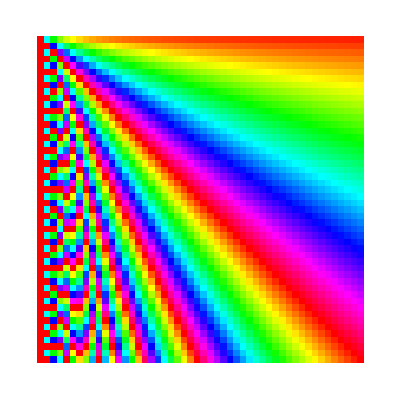

```mathematica
ArrayPlot[Table[Hue[i/j],{i,50},{j,50}]]
```

Q9. Make an array plot of the lengths of Roman numeral strings in a multiplication table up to 100×100.

```mathematica
ArrayPlot[StringLength[RomanNumeral[Table[i j,{i,100},{j,100}]]]]
```

-Graphics-

## Extended Questions

+Q1. Make a 20×20 addition table.

```mathematica
Table[i+j,{i,20},{j,20}]
```

{{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21},{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22},{4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23},{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25},{7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26},{8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27},{9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28},{10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29},{11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},{12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31},{13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32},{14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33},{15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34},{16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35},{17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36},{18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37},{19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38},{20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39},{21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}}

+Q2. Make a 10×10 grid of randomly coloured random integers between 0 and 10 that have random size up to 32.

```mathematica
Grid[Table[Style[RandomInteger[10],RandomInteger[32],RandomColor[]],10,10]]
```

10 | 2 | 4 | 1 | 10 | 6 | 10 | 5 | 0 | 6
8 | 3 | 3 | 7 | 5 | 5 | 1 | 10 | 6 | 3
6 | 10 | 5 | 5 | 2 | 6 | 0 | 1 | 9 | 2
0 | 5 | 6 | 5 | 3 | 9 | 6 | 7 | 5 | 3
4 | 0 | 8 | 0 | 0 | 5 | 0 | 6 | 5 | 4
9 | 8 | 2 | 7 | 3 | 2 | 7 | 3 | 8 | 9
10 | 10 | 0 | 4 | 7 | 2 | 3 | 9 | 10 | 7
3 | 5 | 3 | 9 | 5 | 0 | 0 | 1 | 9 | 2
2 | 0 | 8 | 1 | 9 | 3 | 8 | 2 | 1 | 8
3 | 7 | 0 | 0 | 4 | 10 | 8 | 1 | 4 | 10